```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

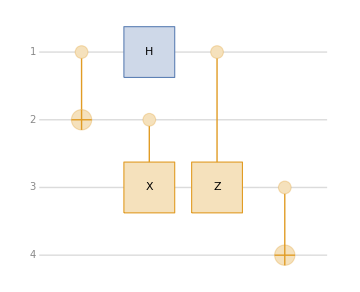

```mathematica
stateTele = QuantumCircuitOperator[
	{QuantumOperator["CNOT", {1, 2}], 
	QuantumOperator["Hadamard", {1}],
	QuantumOperator["CX", {2, 3}],
	QuantumOperator["CZ", {1, 3}],
	QuantumOperator["CNOT", {3, 4}]
	}];
stateTele ["Diagram"]
```

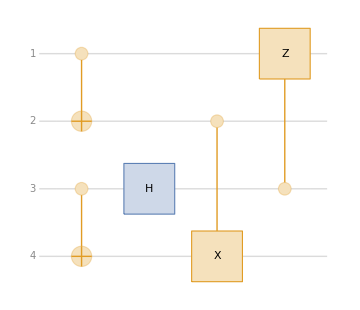

```mathematica
cnotTele = QuantumCircuitOperator[
	{QuantumOperator["CNOT", {1, 2}], 
	QuantumOperator["CNOT", {3, 4}],
	QuantumOperator["Hadamard", {3}],
	QuantumOperator["CX", {2, 4}],
	QuantumOperator["CZ", {3, 1}]
	}];
cnotTele ["Diagram"]
```

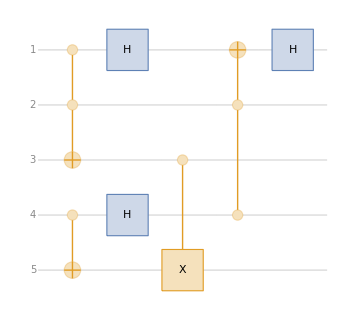

```mathematica
toffoliTele = QuantumCircuitOperator[
	{QuantumOperator["Toffoli", {1, 2, 3}], 
	QuantumOperator["CNOT", {4, 5}],
	QuantumOperator["Hadamard", {4}],
	QuantumOperator["CX", {3, 5}],
	QuantumOperator["Hadamard", {1}],
	QuantumOperator["Toffoli", {4, 2, 1}],
	QuantumOperator["Hadamard", {1}]
	}];
toffoliTele ["Diagram"]
```

```mathematica
normalizationConditions = {
Abs[]^2 + Abs[]^2 == 1,
Abs[]^2+ Abs[]^2 == 1,
Abs[]^2+ Abs[]^2 == 1,
};
```

```mathematica
Fidelity[st_, ma_] := ConjugateTranspose[st["State"]].ma["DensityMatrix"].st["State"];
```

```mathematica
phi={{-Graphics-, QuantumState}}[{,}];
psi={{-Graphics-, QuantumState}}[{,}];
bell = QuantumState["Bell"];
depolarized = QuantumState[IdentityMatrix[4]/4];
noisyBell = QuantumState[(1 -p)bell["DensityMatrix"] + p*IdentityMatrix[4]/4];
```

```mathematica
idealInputState = QuantumTensorProduct[{phi, bell, psi}];
idealOutputState = QuantumPartialTrace[cnotTele[idealInputState], {2, 3}];
```

```mathematica
knownIdealOutput = QuantumState[{, , ,}];
```

```mathematica
phiDensity = QuantumState[phi["DensityMatrix"]];
```

```mathematica
psiDensity = QuantumState[psi["DensityMatrix"]];
```

```mathematica
depolarizedInputState = QuantumTensorProduct[{phiDensity, depolarized, psiDensity}];
Head[depolarizedInputState]
```

QuantumState

QuantumState::undefprop: property QuantumBasis is undefined for this state

```mathematica
Head[cnotTele[depolarizedInputState]]
```

QuantumState

```mathematica
depolarizedOutputState = QuantumPartialTrace[cnotTele[depolarizedInputState], {2, 3}];
```

```mathematica
cnotTele[idealInputState]["Formula"]
```

(α_0 β_0)/2 0000+(α_0 β_1)/2 0001+(α_0 β_0)/2 0010+(α_0 β_1)/2 0011+(α_0 β_0)/2 0100+(α_0 β_1)/2 0101-1/2 α_0 β_00110-1/2 α_0 β_10111+(α_1 β_1)/2 1000+(α_1 β_0)/2 1001+(α_1 β_1)/2 1010+(α_1 β_0)/2 1011+(α_1 β_1)/2 1100+(α_1 β_0)/2 1101-1/2 α_1 β_11110-1/2 α_1 β_01111

```mathematica
noisyInputState = QuantumTensorProduct[{phiDensity, noisyBell, psiDensity}];
noisyOutputState = QuantumPartialTrace[cnotTele[noisyInputState], {2, 3}];
```

```mathematica
depSimp = FullSimplify[Normal[depolarizedOutputState["DensityMatrix"]], normalizationConditions];
goodSimp = FullSimplify[Normal[idealOutputState["DensityMatrix"]], normalizationConditions];
noiseSimp = FullSimplify[Normal[noisyOutputState["DensityMatrix"]], normalizationConditions, Assumptions-> 0<= p <= 1];
```

```mathematica
fidelity = FullSimplify[Fidelity[knownIdealOutput, depolarizedOutputState], normalizationConditions]
```

1/2 (Abs[α_0]^4+Abs[α_1]^4) (1+2 Abs[β_1]^2-2 Abs[β_1]^4+Conjugate[β_1]^2 β_0^2+Conjugate[β_0]^2 β_1^2)

```mathematica
Minimize[{fidelity, Abs[]^2 + Abs[]^2 == 1,Abs[]^2+ Abs[]^2 == 1}, {, , , } ]
```

{1/4,{α_0→-1/(√2),α_1→-1/(√2),β_0→0,β_1→-1}}

```mathematica
zeroState = QuantumState[{{1, 0}, {0, 0}}]
depolarizedInputState' = QuantumTensorProduct[{phiDensity, depolarized, zeroState}];
depolarizedOutputState' = QuantumPartialTrace[stateTele[depolarizedInputState'], {1, 2}];
FullSimplify[Normal[depolarizedOutputState'["DensityMatrix"]], normalizationConditions];
knownIdealOutput' = QuantumState[{, 0, 0, }]
FullSimplify[Fidelity[knownIdealOutput', depolarizedOutputState'], normalizationConditions]
```

QuantumState[…]

```mathematica
QuantumState[…]
```

QuantumState[…]

1/2

```mathematica
targetState = QuantumState[{,}];
```

```mathematica
targetStateDensity = QuantumState[targetState["DensityMatrix"]];
idealInputState2 = QuantumTensorProduct[{phiDensity, psiDensity, bell, targetStateDensity}];
depolarizedInputState2= QuantumTensorProduct[{phiDensity,psiDensity, depolarized, targetStateDensity}];
```

```mathematica
idealOutputState2 = QuantumPartialTrace[toffoliTele[idealInputState2], {3, 4}]
```

QuantumState[SparseArray[<64>, {8, 8}], QuantumBasis[<|Input -> QuditBasis[<|{QuditName[I, Dual -> False], 1} -> 1|>], Output -> QuditBasis[<|{QuditName[0, Dual -> False], 1} -> SparseArray[<1>, {2}], {QuditName[1, Dual -> False], 1} -> SparseArray[<1>, {2}], {«2»} -> <<10>>y[«2»], «2», {QuditName[1, Dual -> False], 3} -> SparseArray[<1>, {2}]|>], «2», ParameterSpec -> {}|>]]

```mathematica
idealInputStateVector2 = QuantumTensorProduct[{phi,psi, bell, targetState}];
idealOutputStateVector2= toffoliTele[idealInputStateVector2];
idealOutputDensityMatrix2 = QuantumPartialTrace[QuantumState[idealOutputStateVector2["DensityMatrix"]], {3, 4}];
idealOutputDensityMatrixSimp2 =FullSimplify[Normal[idealOutputDensityMatrix2["DensityMatrix"]], normalizationConditions];
knownOutputState2 = QuantumState[{,,,,,,,}];
FullSimplify[Fidelity[knownOutputState2, idealOutputDensityMatrix2], normalizationConditions]
```

1

```mathematica
depolarizedInputState2 = QuantumTensorProduct[{phiDensity,psiDensity, depolarized, targetState}];
depolarizedOutputState2= QuantumPartialTrace[toffoliTele[depolarizedInputState2], {3, 4}];
```

```mathematica
QuantumState[FullSimplify[Normal[depolarizedOutputState2["DensityMatrix"]], normalizationConditions]]["Formula"]
```

1/2 (-1+Abs[α_1]^2) (-1+Abs[β_1]^2)000000+1/2 Abs[α_0 β_0]^2 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)000001-1/2 (-1+Abs[α_1]^2) Conjugate[β_1] β_0000010+1/2 Abs[α_0]^2 Conjugate[β_1] β_0 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)000011-1/2 (-1+Abs[β_1]^2) Conjugate[α_1] α_0000100+1/2 Abs[β_0]^2 Conjugate[α_1] α_0 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)000101+1/2 Abs[α_0 β_0]^2 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)001000+1/2 (-1+Abs[α_1]^2) (-1+Abs[β_1]^2)001001+1/2 Abs[α_0]^2 Conjugate[β_1] β_0 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)001010-1/2 (-1+Abs[α_1]^2) Conjugate[β_1] β_0001011+1/2 Abs[β_0]^2 Conjugate[α_1] α_0 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)001100-1/2 (-1+Abs[β_1]^2) Conjugate[α_1] α_0001101-1/2 (-1+Abs[α_1]^2) Conjugate[β_0] β_1010000+1/2 Abs[α_0]^2 Conjugate[β_0] β_1 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)010001-1/2 (-1+Abs[α_1]^2) Abs[β_1]^2010010+1/2 Abs[α_0 β_1]^2 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)010011+1/2 Conjugate[α_1] Conjugate[β_0] α_0 β_1010100+1/2 Conjugate[α_1] Conjugate[β_0] α_0 β_1 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)010101+1/2 Abs[α_0]^2 Conjugate[β_0] β_1 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)011000-1/2 (-1+Abs[α_1]^2) Conjugate[β_0] β_1011001+1/2 Abs[α_0 β_1]^2 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)011010-1/2 (-1+Abs[α_1]^2) Abs[β_1]^2011011+1/2 Conjugate[α_1] Conjugate[β_0] α_0 β_1 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)011100+1/2 Conjugate[α_1] Conjugate[β_0] α_0 β_1011101-1/2 (-1+Abs[β_1]^2) Conjugate[α_0] α_1100000+1/2 Abs[β_0]^2 Conjugate[α_0] α_1 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)100001+1/2 Conjugate[α_0] Conjugate[β_1] α_1 β_0100010+1/2 Conjugate[α_0] Conjugate[β_1] α_1 β_0 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)100011-1/2 Abs[α_1]^2 (-1+Abs[β_1]^2)100100+1/2 Abs[α_1 β_0]^2 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)100101+1/2 Abs[β_0]^2 Conjugate[α_0] α_1 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)101000-1/2 (-1+Abs[β_1]^2) Conjugate[α_0] α_1101001+1/2 Conjugate[α_0] Conjugate[β_1] α_1 β_0 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)101010+1/2 Conjugate[α_0] Conjugate[β_1] α_1 β_0101011+1/2 Abs[α_1 β_0]^2 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)101100-1/2 Abs[α_1]^2 (-1+Abs[β_1]^2)101101+1/2 Abs[α_1 β_1]^2110110+1/2 Abs[α_1 β_1]^2 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)110111+1/2 Abs[α_1 β_1]^2 (Conjugate[γ_1] γ_0+Conjugate[γ_0] γ_1)111110+1/2 Abs[α_1 β_1]^2111111

```mathematica
fidelity2 = FullSimplify[Fidelity[knownOutputState2, depolarizedOutputState2], normalizationConditions]
```

-1/2 (1-2 Abs[α_1 β_1]^2+2 Abs[α_1 β_1]^4) (-1-2 Abs[γ_1]^2+2 Abs[γ_1]^4-Conjugate[γ_1]^2 γ_0^2-Conjugate[γ_0]^2 γ_1^2)